```mathematica
rollRate[t_,a_,v0_]:=a*t+v0
roll[t_,a_,v0_,r0_] := a*t^2/2+v0*t+ r0
PIDStep[Prop_,Int_,Deriv_][{SP_,PV_,e0_,ii0_},dt_]:=Prop*(SP-PV)+Int*(ii0+dt*(SP-PV))+Deriv*(SP-PV - e0)/dt
```

```mathematica
RollPIDStep[Prop_,Int_,Deriv_][{tau0_,v0_,r0_,e0_,ii0_},dt_]:={
PIDStep[Prop,Int,Deriv][{roll[dt,tau0,v0,r0],r0,e0,ii0},dt],
rollRate[dt,tau0,v0],
roll[dt,tau0,v0,r0],
roll[dt,tau0,v0,r0]-r0,
ii0+dt*(roll[dt,tau0,v0,r0]-r0)
}
```

```mathematica
RollPIDEvol[dt_,T_][Prop_,Int_,Deriv_][tau0_,v0_,r0_]:=FoldList[RollPIDStep[Prop,Int,Deriv],{tau0,v0,r0,0,0},Table[dt,{i,1,T/dt,1}]]
```

```mathematica
data[dt_,T_,i_][Prop_,Int_,Deriv_][tau0_,v0_,r0_]:=Transpose@{Range[0,T,dt],(#1[[i]])&/@(RollPIDEvol[dt,T][Prop,Int,Deriv][tau0,v0,r0])}
```

```mathematica
(* PlotRange->All, Filling->Axis *)
```

```mathematica
RollPIDPlot[dt_,T_,i_][Prop_,Int_,Deriv_][tau0_,v0_,r0_]:= ListPlot[
Legended[
data[dt,T,i][Prop,Int,Deriv][tau0,v0,r0],
"Proportional="<>ToString[Prop]<>"\nIntegral="<>ToString[Int]<>"\nDerivative="<>ToString[Deriv]
],PlotLabel->If[i==1,"Torque:",If[i==2,"Roll rate:",If[i==3,"Roll:","Unknown:"]]]<>" tau0="<>ToString[tau0]<>" & v0="<>ToString[v0]<>" & r0="<>ToString[r0]]
```

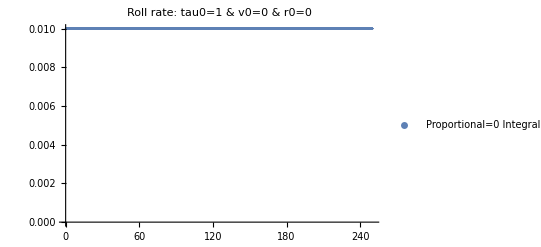

```mathematica
RollPIDPlot[0.01,250,2][0,0,0][1,0,0]
```

```mathematica
(* Observation: Proportional > 0 ==> Diverges *)
```

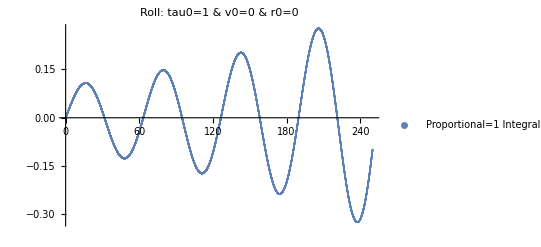

```mathematica
RollPIDPlot[0.01,250,3][1,-1,-1][1,0,0]
```

```mathematica
(* Observation: Proportional = 0 ==> Oscillates *)
```

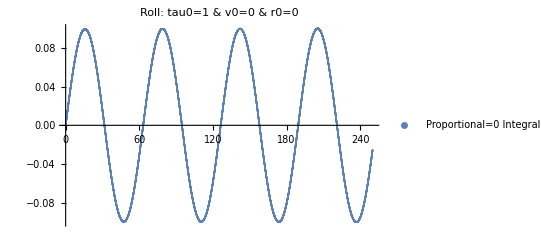

```mathematica
RollPIDPlot[0.01,250,3][0,-1,-1][1,0,0]
```

```mathematica
(* Observation: Integral >= 0 ==> Increases *)
```

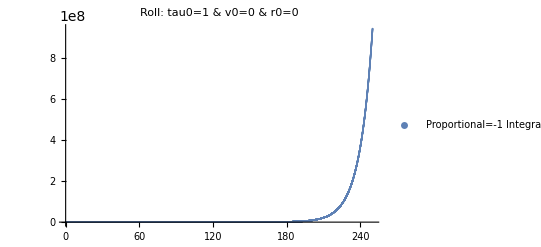

```mathematica
RollPIDPlot[0.01,250,3][-1,1,-1][1,0,0]
```

```mathematica
(* Observation: Higher values of derivative slowly increase the frecuency *)
```

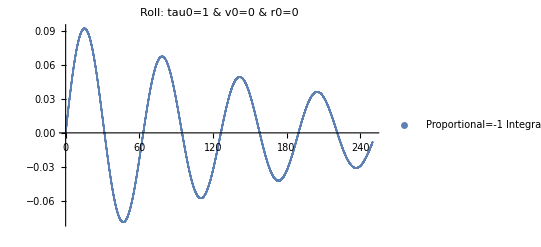

```mathematica
RollPIDPlot[0.01,250,3][-1,-1,-1][1,0,0]
```

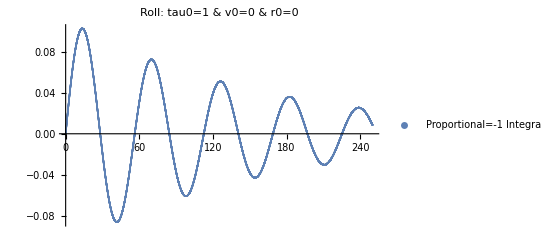

```mathematica
RollPIDPlot[0.01,250,3][-1,-1,20][1,0,0]
```

```mathematica
(* Observation: If proportional and integral are close, then we get oscillations *)
```

```mathematica
RollPIDPlot[0.01,250,3][-1,-1,-1][1,0,0]
```

-Graphics-

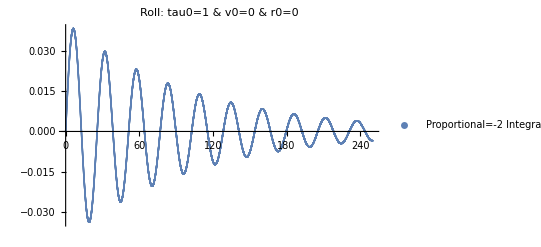

```mathematica
RollPIDPlot[0.01,250,3][-2,-6,0][1,0,0]
```

```mathematica
(* Observation: But if proportional is much larger than integral, we remove the oscillations *)
```

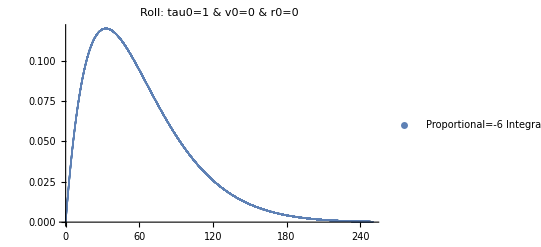

```mathematica
RollPIDPlot[0.01,250,3][-6,-0.1,-3][1,0,0]
```

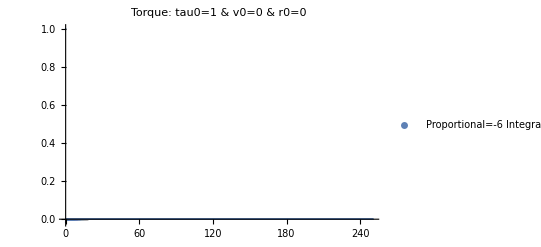

```mathematica
RollPIDPlot[0.01,250,1][-6,-0.1,-3][1,0,0]
```

```mathematica
(* Observation: Both the oscillating and asymptotic control converge to original roll angle *)
```

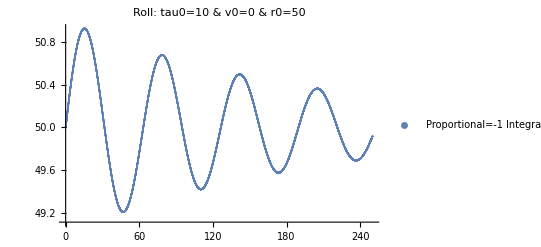

```mathematica
RollPIDPlot[0.01,250,3][-1,-1,-1][10,0,50]
```

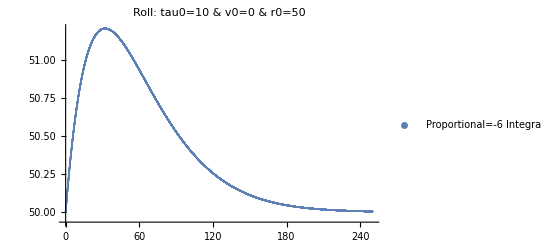

```mathematica
RollPIDPlot[0.01,250,3][-6,-0.1,0][10,0,50]
```

```mathematica
(* Observation: Nevertheless, large values of torque are stabilized quickly with an appropriate initial roll *)
```

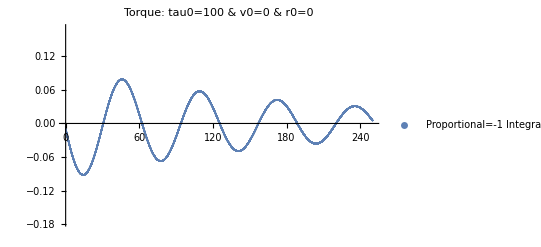

```mathematica
RollPIDPlot[0.01,250,1][-1,-1,-1][100,0,0]
```

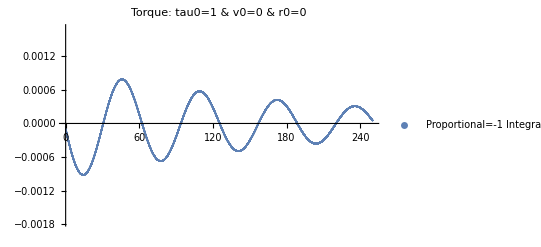

```mathematica
RollPIDPlot[0.01,250,1][-1,-1,-1][1,0,0]
```

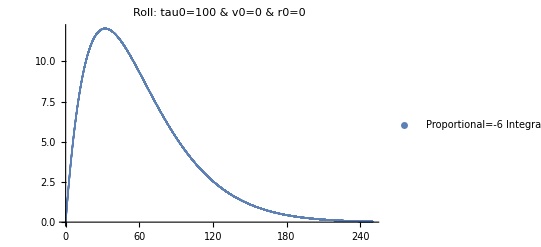

```mathematica
RollPIDPlot[0.01,250,3][-6,-0.1,0][100,0,0]
```

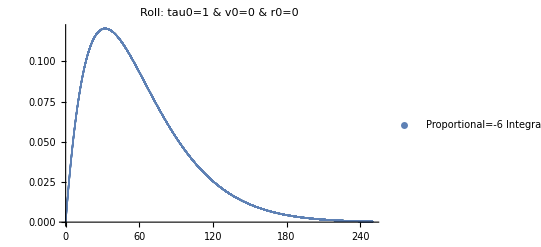

```mathematica
RollPIDPlot[0.01,250,3][-6,-0.1,0][1,0,0]
```

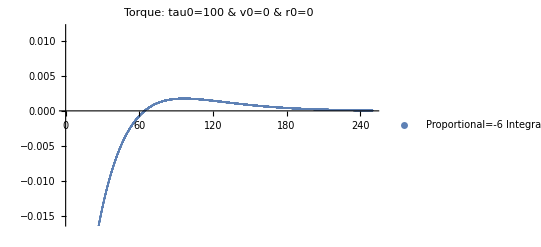

```mathematica
RollPIDPlot[0.01,250,1][-6,-0.1,0][100,0,0]
```

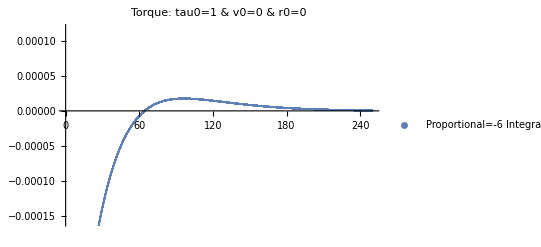

```mathematica
RollPIDPlot[0.01,250,1][-6,-0.1,0][1,0,0]
```

```mathematica
(* Finding invariant *)
```

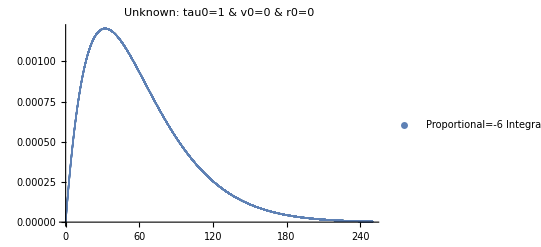

```mathematica
RollPIDPlot[0.01,250,5][-6,-0.1,0][1,0,0]
```

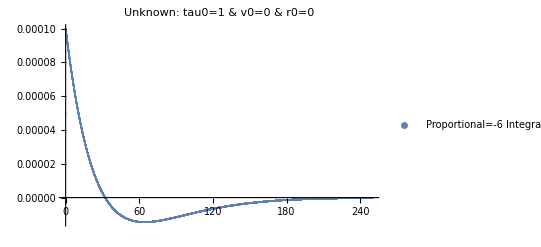

```mathematica
RollPIDPlot[0.01,250,4][-6,-0.1,0][1,0,0]
```

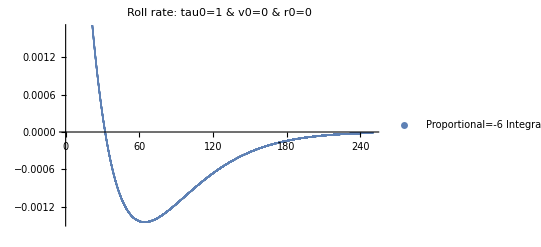

```mathematica
RollPIDPlot[0.01,250,2][-6,-0.1,0][1,0,0]
```

```mathematica
Evol1:=Simplify /@FoldList[RollPIDStep[Prop,Int,0],{1,0,0,0,0},Table[t,{i,1,10,1}]]
```

```mathematica
#1[[1]]&/@Evol1
```

{1,1/2 t^2 (Prop+Int t),1/4 t^2 (Prop^2 t^2+2 Prop (2+Int t^3)+Int t (6+Int t^3)),1/8 t^2 (Prop^3 t^4+Prop^2 t^2 (8+3 Int t^3)+Int t (20+12 Int t^3+Int^2 t^6)+Prop (8+20 Int t^3+3 Int^2 t^6)),1/16 t^2 (Prop^4 t^6+4 Prop^3 t^4 (3+Int t^3)+Prop^2 (32 t^2+42 Int t^5+6 Int^2 t^8)+4 Prop (4+26 Int t^3+12 Int^2 t^6+Int^3 t^9)+Int t (56+76 Int t^3+18 Int^2 t^6+Int^3 t^9)),1/32 t^2 (Prop^5 t^8+Prop^4 t^6 (16+5 Int t^3)+2 Prop^3 t^4 (36+36 Int t^3+5 Int^2 t^6)+2 Prop^2 t^2 (48+150 Int t^3+60 Int^2 t^6+5 Int^3 t^9)+Int t (144+352 Int t^3+168 Int^2 t^6+24 Int^3 t^9+Int^4 t^12)+Prop (32+400 Int t^3+396 Int^2 t^6+88 Int^3 t^9+5 Int^4 t^12)),1/64 t^2 (Prop^6 t^10+2 Prop^5 t^8 (10+3 Int t^3)+Prop^4 t^6 (128+110 Int t^3+15 Int^2 t^6)+4 Prop^3 t^4 (76+164 Int t^3+60 Int^2 t^6+5 Int^3 t^9)+Prop^2 t^2 (256+1512 Int t^3+1224 Int^2 t^6+260 Int^3 t^9+15 Int^4 t^12)+Int t (352+1360 Int t^3+1104 Int^2 t^6+296 Int^3 t^9+30 Int^4 t^12+Int^5 t^15)+2 Prop (32+656 Int t^3+1152 Int^2 t^6+496 Int^3 t^9+70 Int^4 t^12+3 Int^5 t^15)),1/128 t^2 (Prop^7 t^12+Prop^6 t^10 (24+7 Int t^3)+Prop^5 t^8 (200+156 Int t^3+21 Int^2 t^6)+Prop^4 t^6 (704+1220 Int t^3+420 Int^2 t^6+35 Int^3 t^9)+Prop^3 t^4 (1056+4128 Int t^3+2920 Int^2 t^6+600 Int^3 t^9+35 Int^4 t^12)+Prop^2 t^2 (640+6192 Int t^3+8640 Int^2 t^6+3440 Int^3 t^9+480 Int^4 t^12+21 Int^5 t^15)+Int t (832+4672 Int t^3+5808 Int^2 t^6+2528 Int^3 t^9+460 Int^4 t^12+36 Int^5 t^15+Int^6 t^18)+Prop (128+3904 Int t^3+10800 Int^2 t^6+7744 Int^3 t^9+2000 Int^4 t^12+204 Int^5 t^15+7 Int^6 t^18)),1/256 t^2 (Prop^8 t^14+4 Prop^7 t^12 (7+2 Int t^3)+2 Prop^6 t^10 (144+105 Int t^3+14 Int^2 t^6)+8 Prop^5 t^8 (170+255 Int t^3+84 Int^2 t^6+7 Int^3 t^9)+2 Prop^4 t^6 (1536+4620 Int t^3+2970 Int^2 t^6+595 Int^3 t^9+35 Int^4 t^12)+4 Prop^3 t^4 (816+5136 Int t^3+6080 Int^2 t^6+2280 Int^3 t^9+315 Int^4 t^12+14 Int^5 t^15)+2 Prop^2 t^2 (768+11088 Int t^3+24048 Int^2 t^6+15600 Int^3 t^9+3900 Int^4 t^12+399 Int^5 t^15+14 Int^6 t^18)+8 Prop (32+1360 Int t^3+5472 Int^2 t^6+5944 Int^3 t^9+2450 Int^4 t^12+441 Int^5 t^15+35 Int^6 t^18+Int^7 t^21)+Int t (1920+14784 Int t^3+26208 Int^2 t^6+16944 Int^3 t^9+4840 Int^4 t^12+660 Int^5 t^15+42 Int^6 t^18+Int^7 t^21)),1/512 t^2 (Prop^9 t^16+Prop^8 t^14 (32+9 Int t^3)+4 Prop^7 t^12 (98+68 Int t^3+9 Int^2 t^6)+4 Prop^6 t^10 (584+791 Int t^3+252 Int^2 t^6+21 Int^3 t^9)+2 Prop^5 t^8 (3600+9048 Int t^3+5418 Int^2 t^6+1064 Int^3 t^9+63 Int^4 t^12)+2 Prop^4 t^6 (5760+27240 Int t^3+28560 Int^2 t^6+10220 Int^3 t^9+1400 Int^4 t^12+63 Int^5 t^15)+4 Prop^3 t^4 (2336+21792 Int t^3+39400 Int^2 t^6+23600 Int^3 t^9+5740 Int^4 t^12+588 Int^5 t^15+21 Int^6 t^18)+4 Prop^2 t^2 (896+18096 Int t^3+56736 Int^2 t^6+55000 Int^3 t^9+21600 Int^4 t^12+3843 Int^5 t^15+308 Int^6 t^18+9 Int^7 t^21)+Int t (4352+44032 Int t^3+105728 Int^2 t^6+95488 Int^3 t^9+39520 Int^4 t^12+8256 Int^5 t^15+896 Int^6 t^18+48 Int^7 t^21+Int^8 t^24)+Prop (512+28928 Int t^3+159936 Int^2 t^6+246400 Int^3 t^9+149200 Int^4 t^12+41616 Int^5 t^15+5684 Int^6 t^18+368 Int^7 t^21+9 Int^8 t^24)),1/1024 t^2 (Prop^10 t^18+2 Prop^9 t^16 (18+5 Int t^3)+Prop^8 t^14 (512+342 Int t^3+45 Int^2 t^6)+8 Prop^7 t^12 (462+580 Int t^3+180 Int^2 t^6+15 Int^3 t^9)+2 Prop^6 t^10 (7296+16100 Int t^3+9128 Int^2 t^6+1764 Int^3 t^9+105 Int^4 t^12)+4 Prop^5 t^8 (8016+30936 Int t^3+29568 Int^2 t^6+10192 Int^3 t^9+1386 Int^4 t^12+63 Int^5 t^15)+2 Prop^4 t^6 (19456+134640 Int t^3+211800 Int^2 t^6+119000 Int^3 t^9+28280 Int^4 t^12+2898 Int^5 t^15+105 Int^6 t^18)+8 Prop^3 t^4 (3168+41248 Int t^3+106720 Int^2 t^6+94200 Int^3 t^9+35490 Int^4 t^12+6244 Int^5 t^15+504 Int^6 t^18+15 Int^7 t^21)+Prop^2 t^2 (8192+220800 Int t^3+948864 Int^2 t^6+1293760 Int^3 t^9+738000 Int^4 t^12+201096 Int^5 t^15+27440 Int^6 t^18+1800 Int^7 t^21+45 Int^8 t^24)+Int t (9728+125184 Int t^3+391680 Int^2 t^6+472320 Int^3 t^9+268096 Int^4 t^12+79584 Int^5 t^15+12992 Int^6 t^18+1168 Int^7 t^21+54 Int^8 t^24+Int^9 t^27)+2 Prop (512+37120 Int t^3+270336 Int^2 t^6+562688 Int^3 t^9+472640 Int^4 t^12+189216 Int^5 t^15+39200 Int^6 t^18+4288 Int^7 t^21+234 Int^8 t^24+5 Int^9 t^27))}

```mathematica
myFun[n_][t_]:=(1/2)^n*(-6)^n*t^(3*(n-1)+1)
```

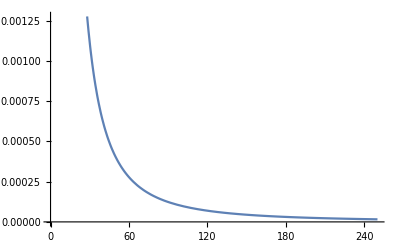
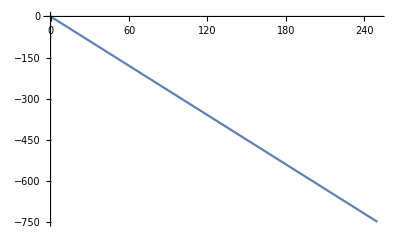
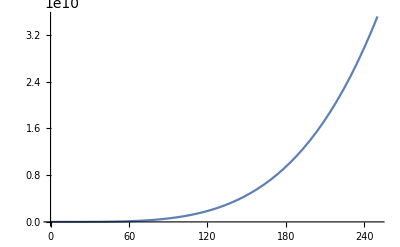
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[myFun[n][t],{t,0,250}] ,{n,0,15}]
```

```mathematica
(* Generates multiple graphs *)
```

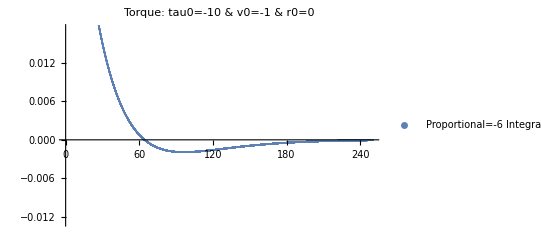
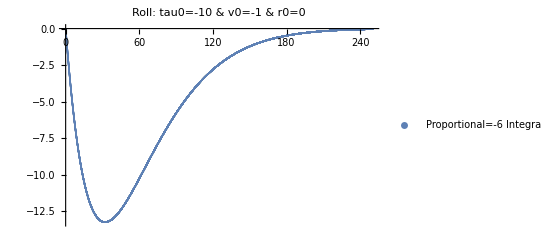
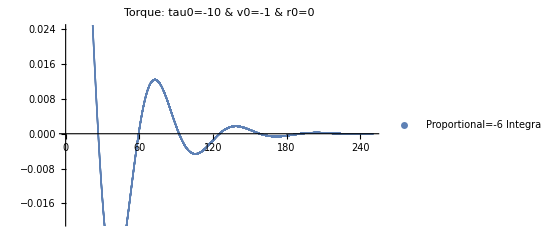
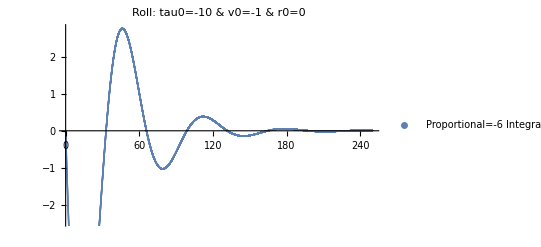
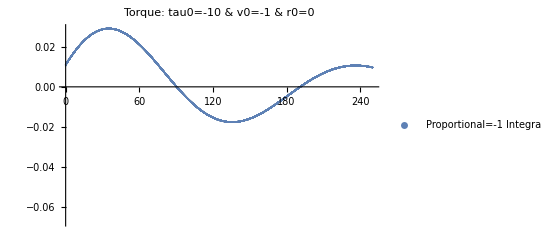
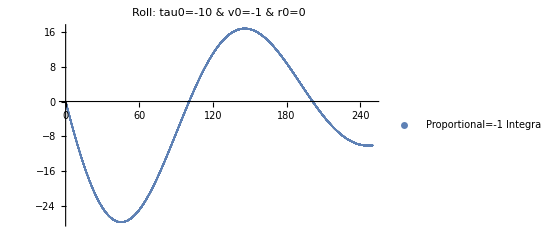
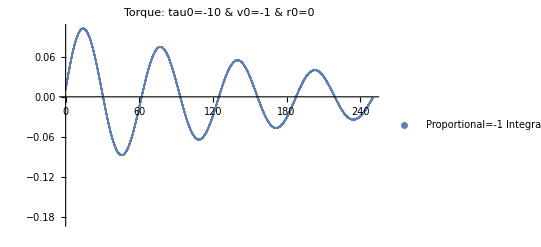
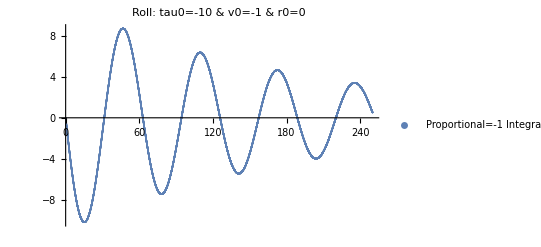
{{{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}},{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}},{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}}},{{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}},{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}},{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}}},{{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}},{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}},{{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}}}}

```mathematica
Table[RollPIDPlot[0.01,250,i][Prop,Int,0][tau0,v0,0],{tau0,-10,10,10},{v0,-1,1,1},{r0,-10,10,10},{Prop,{-6,-1}},{Int,{-0.1,-1}},{i,{1,3}}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* https://oscarliang.com/quadcopter-pid-explained-tuning/ *)
```

```mathematica
(* Do not run (they exist): GraphicsGrid[myPlots], Show[myPlots], GraphicsRow[myPlots] *)
```